```mathematica
Quit[]
```

```mathematica
Directory[]
```

C:\Users\Jieyu You\Documents

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Jieyu You\Documents\GitHub\circular-waveguide

```mathematica
atom=1;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];
r[1]=0.λ0;
r[2]=-0.6λ0;
ratio=2;
γ[2]=1/ratio;(*lower*)
γ[3]=ratio; (*higher*)
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])];(*KroneckerDelta[j,l]; atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]+r[k])](*KroneckerDelta[j,5-l]*); 
Λ[i_,j_,k_,l_]:=√(γ[j]γ[l])Sin[k0(r[i]-r[k])]/2;
δω=0;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

solsq=NDSolve[{ρ'[t]==-0.5*sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(sh^2+1)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-I Sum[ Λ[i,j,k,l](σ[i,j,1].σ[k,l,0].ρ[t]-ρ[t].σ[i,j,1].σ[k,l,0])Exp[I(ω[j]-ω[l])t],{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,100}];
solth=NDSolve[{ρ'[t]==-0.*sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(sh^2+1)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-I Sum[ Λ[i,j,k,l](σ[i,j,1].σ[k,l,0].ρ[t]-ρ[t].σ[i,j,1].σ[k,l,0])Exp[I(ω[j]-ω[l])t],{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,100}];
```

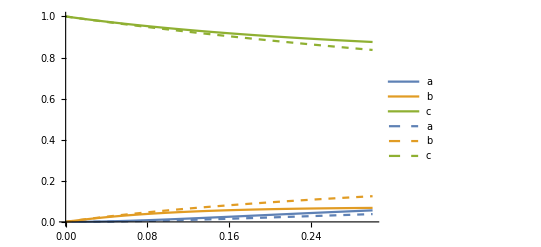

```mathematica
T=0.3;
sq=Plot[{a[1,1][t]/.solsq,a[2,2][t]/.solsq,a[3,3][t]/.solsq},{t,0,T},PlotLegends->{"a","b","c"},PlotRange->All];
th=Plot[{a[1,1][t]/.solth,a[2,2][t]/.solth,a[3,3][t]/.solth},{t,0,T},PlotLegends->{"a","b","c"}, PlotStyle->Dashed,PlotRange->All];
Show[sq, th]
```

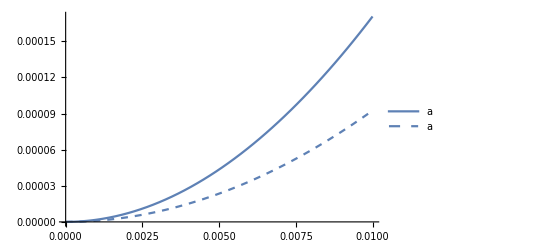

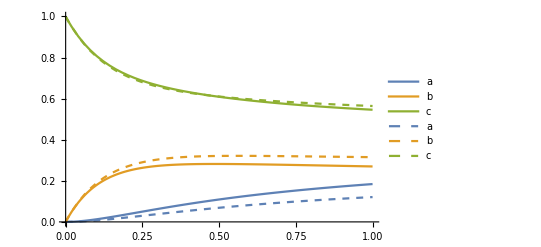

```mathematica
T=0.01;
sq=Plot[{a[1,1][t]/.solsq},{t,0,T},PlotLegends->{"a","b","c"},PlotRange->All];
th=Plot[{a[1,1][t]/.solth},{t,0,T},PlotLegends->{"a","b","c"}, PlotStyle->Dashed,PlotRange->All];
Show[sq, th]
```

```mathematica
ss=Chop[ρ[t]/.solsq/.t->100,10^-5][[1]];
ss//MatrixForm
```

(0.0351181 | 0 | 0.00142973+0.00106558 ⅈ | 0 | -0.000308453-0.000156662 ⅈ | 0 | 0.00121638-0.000122436 ⅈ | 0 | -0.0140599-0.000807215 ⅈ
0 | 0.0599819-0.000108244 ⅈ | 0 | -0.00388538 | 0 | 0.0166305-0.00270757 ⅈ | 0 | -0.00440507-0.00229607 ⅈ | 0
0.00121638+0.000122436 ⅈ | 0 | 0.0859669+0.00114944 ⅈ | 0 | -0.000817644+0.0000899631 ⅈ | 0 | 0.00132359 | 0 | -0.0116526-0.00292318 ⅈ
0 | -0.00451162 | 0 | 0.0599819+0.000108244 ⅈ | 0 | -0.00491652+0.00279167 ⅈ | 0 | 0.0170781-0.000590036 ⅈ | 0
-0.000308453+0.000156662 ⅈ | 0 | -0.00107043-0.000399318 ⅈ | 0 | 0.0825424 | 0 | -0.000817644-0.0000899631 ⅈ | 0 | 0.00795779+0.00686071 ⅈ
0 | 0.0170781+0.000590036 ⅈ | 0 | -0.00440507+0.00229607 ⅈ | 0 | 0.157283+0.000349582 ⅈ | 0 | 0.00419197 | 0
0.00142973-0.00106558 ⅈ | 0 | 0.00219356 | 0 | -0.00107043+0.000399318 ⅈ | 0 | 0.0859669-0.00114944 ⅈ | 0 | -0.0149162+0.000624871 ⅈ
0 | -0.00491652-0.00279167 ⅈ | 0 | 0.0166305+0.00270757 ⅈ | 0 | 0.00528564 | 0 | 0.157283-0.000349582 ⅈ | 0
-0.0140599+0.000807215 ⅈ | 0 | -0.0149162-0.000624871 ⅈ | 0 | 0.00795779-0.00686071 ⅈ | 0 | -0.0116526+0.00292318 ⅈ | 0 | 0.275875)

```mathematica
(*Partial trace: <a1...ai...an|ρ|a1...ai'...an>, sum all but i, ρ[x,y], x is state |dim-x>, y is state |dim-y>. sum dim-x,dim-y from 0 to dim-1 (x from 1 to dim), with dim-x's ith digit = ai, dim-y's ith digit = ai', other digits the same, and ai correspond to level-ai*)
ss=Chop[ρ[t]/.solsq/.t->100,10^-5][[1]];
m=2;
pt=Chop[Table[Sum[ss[[x,y]]Boole[Drop[IntegerDigits[dim-x,level,atom],{m}]==Drop[IntegerDigits[dim-y,level,atom],{m}]]Boole[IntegerDigits[dim-x,level,atom][[m]]==level-i]Boole[IntegerDigits[dim-y,level,atom][[m]]==level-j],{x,1,dim},{y,1,dim}],{i,1,level},{j,1,level}],10^-5];
pt//MatrixForm
Tr[pt]
(*pop inversion except degenerate  *)
(*identical to single atom except degenerate case*)
(*draw: pop vs dipole, pop vs position*)
```

(0.181067-0.0010412 ⅈ | 0 | -0.018403+0.00448212 ⅈ
0 | 0.299808-0.000457826 ⅈ | 0
-0.0148413+0.00534168 ⅈ | 0 | 0.519125+0.00149902 ⅈ)

1.-1.0842×10^-17 ⅈ

```mathematica
Table[pt[[level- IntegerDigits[dim-x,level,atom][[1]] , level-IntegerDigits[dim-y,level,atom][[1]] ]]*pt[[level- IntegerDigits[dim-x,level,atom][[2]] , level-IntegerDigits[dim-y,level,atom][[2]]]],{x,1,dim},{y,1,dim}]//MatrixForm
```

(0.0327841-0.000377053 ⅈ | 0.+0. ⅈ | -0.0033275+0.000830724 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ | -0.0033275+0.000830724 ⅈ | 0.+0. ⅈ | 0.000318579-0.000164968 ⅈ
0.+0. ⅈ | 0.0542848-0.000395056 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ | 0 | 0.+0. ⅈ | -0.00551529+0.0013522 ⅈ | 0.+0. ⅈ
-0.00268171+0.000982654 ⅈ | 0.+0. ⅈ | 0.093998-0.000269089 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ | 0.000249182-0.000164823 ⅈ | 0.+0. ⅈ | -0.00956016+0.0022992 ⅈ
0.+0. ⅈ | 0 | 0.+0. ⅈ | 0.0542848-0.000395056 ⅈ | 0.+0. ⅈ | -0.00551529+0.0013522 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ
0 | 0.+0. ⅈ | 0 | 0.+0. ⅈ | 0.0898844-0.00027452 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ | 0
0.+0. ⅈ | 0 | 0.+0. ⅈ | -0.0044471+0.00160827 ⅈ | 0.+0. ⅈ | 0.155638+0.00021175 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ
-0.00268171+0.000982654 ⅈ | 0.+0. ⅈ | 0.000249182-0.000164823 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ | 0.093998-0.000269089 ⅈ | 0.+0. ⅈ | -0.00956016+0.0022992 ⅈ
0.+0. ⅈ | -0.0044471+0.00160827 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ | 0 | 0.+0. ⅈ | 0.155638+0.00021175 ⅈ | 0.+0. ⅈ
0.000191731-0.000158555 ⅈ | 0.+0. ⅈ | -0.00771252+0.00275075 ⅈ | 0.+0. ⅈ | 0 | 0.+0. ⅈ | -0.00771252+0.00275075 ⅈ | 0.+0. ⅈ | 0.269489+0.00155636 ⅈ)

```mathematica
IntegerDigits[dim-1,level,atom][[1]]
```

2

```mathematica
pt[[1,1]]
```

0.698804

```mathematica
Chop[Out[36]-Out[30],10^-5]//MatrixForm
```

(-0.00233398-0.000377053 ⅈ | 0 | -0.00475723-0.000234857 ⅈ | 0 | 0.000308453+0.000156662 ⅈ | 0 | -0.00454388+0.00095316 ⅈ | 0 | 0.0143785+0.000642246 ⅈ
0 | -0.00569713-0.000286812 ⅈ | 0 | 0.00388538 | 0 | -0.0166305+0.00270757 ⅈ | 0 | -0.00111023+0.00364827 ⅈ | 0
-0.00389809+0.000860218 ⅈ | 0 | 0.00803111-0.00141853 ⅈ | 0 | 0.000817644-0.0000899631 ⅈ | 0 | -0.00107441-0.000164823 ⅈ | 0 | 0.00209248+0.00522237 ⅈ
0 | 0.00451162 | 0 | -0.00569713-0.0005033 ⅈ | 0 | -0.000598775-0.00143947 ⅈ | 0 | -0.0170781+0.000590036 ⅈ | 0
0.000308453-0.000156662 ⅈ | 0 | 0.00107043+0.000399318 ⅈ | 0 | 0.00734205-0.00027452 ⅈ | 0 | 0.000817644+0.0000899631 ⅈ | 0 | -0.00795779-0.00686071 ⅈ
0 | -0.0170781-0.000590036 ⅈ | 0 | -0.00004203-0.000687795 ⅈ | 0 | -0.00164492-0.000137832 ⅈ | 0 | -0.00419197 | 0
-0.00411144+0.00204823 ⅈ | 0 | -0.00194438-0.000164823 ⅈ | 0 | 0.00107043-0.000399318 ⅈ | 0 | 0.00803111+0.000880353 ⅈ | 0 | 0.005356+0.00167432 ⅈ
0 | 0.000469422+0.00439994 ⅈ | 0 | -0.0166305-0.00270757 ⅈ | 0 | -0.00528564 | 0 | -0.00164492+0.000561332 ⅈ | 0
0.0142516-0.00096577 ⅈ | 0 | 0.00720364+0.00337563 ⅈ | 0 | -0.00795779+0.00686071 ⅈ | 0 | 0.00394012-0.000172422 ⅈ | 0 | -0.00638619+0.00155636 ⅈ)

```mathematica
Quit[]
```

```mathematica
(*data for positions*)
atom=2;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];


A=Table[
r[1]=0λ0;
r[2]=-d λ0;
r[3]=-2λ0;
ratio=0.5;
γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]; (*atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]; 
δω=10;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

solsq=NDSolve[{ρ'[t]==-0.5sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(sh^2+1)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,100}];
ss=Chop[ρ[t]/.solsq/.t->100,10^-5][[1]];
m=1;
pt=Chop[Table[Sum[ss[[x,y]]Boole[Drop[IntegerDigits[dim-x,level,atom],{m}]==Drop[IntegerDigits[dim-y,level,atom],{m}]]Boole[IntegerDigits[dim-x,level,atom][[m]]==level-i]Boole[IntegerDigits[dim-y,level,atom][[m]]==level-j],{x,1,dim},{y,1,dim}],{i,1,level},{j,1,level}],10^-5];m=2;
pt2=Chop[Table[Sum[ss[[x,y]]Boole[Drop[IntegerDigits[dim-x,level,atom],{m}]==Drop[IntegerDigits[dim-y,level,atom],{m}]]Boole[IntegerDigits[dim-x,level,atom][[m]]==level-i]Boole[IntegerDigits[dim-y,level,atom][[m]]==level-j],{x,1,dim},{y,1,dim}],{i,1,level},{j,1,level}],10^-5];{d,pt[[1,1]],pt[[2,2]],pt[[3,3]],pt2[[1,1]],pt2[[2,2]],pt2[[3,3]]},{d,0,0.5,0.01}]
```

{{0.,0.698804,0,0.301196,0.698804,0,0.301196},{0.01,0.694322,0.00336238,0.302315,0.694322,0.00336238,0.302315},{0.02,0.698029,0.000519441,0.301452,0.698029,0.000519441,0.301452},{0.03,0.698565,0.000148234,0.301287,0.698565,0.000148234,0.301287},{0.04,0.698631,0.000103842,0.301265,0.698631,0.000103842,0.301265},{0.05,0.698649,0.0000912209,0.30126,0.698649,0.0000912209,0.30126},{0.06,0.698661,0.0000835539,0.301256,0.698661,0.0000835539,0.301256},{0.07,0.698672,0.000076242,0.301251,0.698672,0.000076242,0.301251},{0.08,0.698685,0.000068555,0.301246,0.698685,0.000068555,0.301246},{0.09,0.698698,0.0000520403,0.301241,0.698698,0.0000520403,0.301241},{0.1,0.698712,0.0000456848,0.301235,0.698712,0.0000456848,0.301235},{0.11,0.698725,0.0000395924,0.30123,0.698725,0.0000395924,0.30123},{0.12,0.698736,0.0000339865,0.301225,0.698736,0.0000339865,0.301225},{0.13,0.698747,0.0000289311,0.30122,0.698747,0.0000289311,0.30122},{0.14,0.698756,0.0000244816,0.301216,0.698756,0.0000244816,0.301216},{0.15,0.698764,0.0000120923,0.301205,0.698764,0.0000120923,0.301205},{0.16,0.698771,0.0000104782,0.301203,0.698771,0.0000104782,0.301203},{0.17,0.698767,0,0.301202,0.698767,0,0.301202},{0.18,0.698773,0,0.301201,0.698773,0,0.301201},{0.19,0.698778,0,0.301201,0.698778,0,0.301201},{0.2,0.698781,0,0.3012,0.698781,0,0.3012},{0.21,0.698784,0,0.301199,0.698784,0,0.301199},{0.22,0.698786,0,0.301199,0.698786,0,0.301199},{0.23,0.698787,0,0.301199,0.698787,0,0.301199},{0.24,0.698788,0,0.301199,0.698788,0,0.301199},{0.25,0.698788,0,0.301199,0.698788,0,0.301199},{0.26,0.698788,0,0.301199,0.698788,0,0.301199},{0.27,0.698787,0,0.301199,0.698787,0,0.301199},{0.28,0.698786,0,0.301199,0.698786,0,0.301199},{0.29,0.698784,0,0.301199,0.698784,0,0.301199},{0.3,0.698781,0,0.3012,0.698781,0,0.3012},{0.31,0.698778,0,0.301201,0.698778,0,0.301201},{0.32,0.698773,0,0.301201,0.698773,0,0.301201},{0.33,0.698767,0,0.301202,0.698767,0,0.301202},{0.34,0.698771,0.0000104783,0.301203,0.698771,0.0000104783,0.301203},{0.35,0.698764,0.0000120919,0.301205,0.698764,0.0000120919,0.301205},{0.36,0.698756,0.0000244813,0.301216,0.698756,0.0000244813,0.301216},{0.37,0.698747,0.000028932,0.30122,0.698747,0.000028932,0.30122},{0.38,0.698736,0.0000339866,0.301225,0.698736,0.0000339866,0.301225},{0.39,0.698725,0.0000395957,0.30123,0.698725,0.0000395957,0.30123},{0.4,0.698712,0.0000456704,0.301235,0.698712,0.0000456704,0.301235},{0.41,0.698698,0.0000520403,0.301241,0.698698,0.0000520403,0.301241},{0.42,0.698685,0.0000685494,0.301246,0.698685,0.0000685494,0.301246},{0.43,0.698672,0.0000762357,0.301251,0.698672,0.0000762357,0.301251},{0.44,0.698661,0.0000835503,0.301256,0.698661,0.0000835503,0.301256},{0.45,0.698649,0.0000912209,0.30126,0.698649,0.0000912209,0.30126},{0.46,0.698631,0.000103842,0.301265,0.698631,0.000103842,0.301265},{0.47,0.698565,0.000148234,0.301287,0.698565,0.000148234,0.301287},{0.48,0.698029,0.000519441,0.301452,0.698029,0.000519441,0.301452},{0.49,0.694322,0.00336238,0.302315,0.694322,0.00336238,0.302315},{0.5,0.698804,0,0.301196,0.698804,0,0.301196}}

```mathematica
Export["position_dep.dat" ,A]
```

position_dep.dat

```mathematica
Quit[]
```

```mathematica
(*data for ratio*)
atom=3;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];


A=Table[
r[1]=0λ0;
r[2]= 0.1λ0;
r[3]=0.2λ0;
ratio=d;
γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]; (*atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]; 
δω=10;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

solsq=NDSolve[{ρ'[t]==-0.5sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(sh^2+1)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,100}];
ss=Chop[ρ[t]/.solsq/.t->100,10^-5][[1]];
m=1;
pt=Chop[Table[Sum[ss[[x,y]]Boole[Drop[IntegerDigits[dim-x,level,atom],{m}]==Drop[IntegerDigits[dim-y,level,atom],{m}]]Boole[IntegerDigits[dim-x,level,atom][[m]]==level-i]Boole[IntegerDigits[dim-y,level,atom][[m]]==level-j],{x,1,dim},{y,1,dim}],{i,1,level},{j,1,level}],10^-5];m=2;
pt2=Chop[Table[Sum[ss[[x,y]]Boole[Drop[IntegerDigits[dim-x,level,atom],{m}]==Drop[IntegerDigits[dim-y,level,atom],{m}]]Boole[IntegerDigits[dim-x,level,atom][[m]]==level-i]Boole[IntegerDigits[dim-y,level,atom][[m]]==level-j],{x,1,dim},{y,1,dim}],{i,1,level},{j,1,level}],10^-5];

m=3;
pt2=Chop[Table[Sum[ss[[x,y]]Boole[Drop[IntegerDigits[dim-x,level,atom],{m}]==Drop[IntegerDigits[dim-y,level,atom],{m}]]Boole[IntegerDigits[dim-x,level,atom][[m]]==level-i]Boole[IntegerDigits[dim-y,level,atom][[m]]==level-j],{x,1,dim},{y,1,dim}],{i,1,level},{j,1,level}],10^-5];{pt[[1,1]],pt[[2,2]],pt[[3,3]],pt2[[1,1]],pt2[[2,2]],pt2[[3,3]]},{d,0.01,2,0.05}];
```

```mathematica
Export["ratio.dat",A]
```

ratio.dat

```mathematica
atom=1;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];



r[1]=0λ0;
r[2]=1 λ0;
r[3]=-2λ0;
ratio=0.5;
γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]; (*atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]+r[k])]; 
δω=0;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

solsq=NDSolve[{ρ'[t]==-0.5sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(sh^2+1)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,100}];
ss=Chop[ρ[t]/.solsq/.t->100,10^-5][[1]];
ss//MatrixForm
```

(0.698793 | 0 | -0.458768
0 | 0 | 0
-0.458768 | 0 | 0.301201)

```mathematica
Quit[]
```

```mathematica
(*γp=cosi-j*)
atom=3;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];
r[1]=0λ0;
r[2]=-0.05λ0;
r[3]=-0.1λ0;
ratio=0.5;
γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]; (*atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]; 
δω=0;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

solsq=NDSolve[{ρ'[t]==-0.5sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(sh^2+1)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,100}];
```

```mathematica
ss=Chop[ρ[t]/.solsq/.t->100,10^-5][[1]];
m=1;
pt=Chop[Table[Sum[ss[[x,y]]Boole[Drop[IntegerDigits[dim-x,level,atom],{m}]==Drop[IntegerDigits[dim-y,level,atom],{m}]]Boole[IntegerDigits[dim-x,level,atom][[m]]==level-i]Boole[IntegerDigits[dim-y,level,atom][[m]]==level-j],{x,1,dim},{y,1,dim}],{i,1,level},{j,1,level}],10^-5];
pt//MatrixForm
Tr[pt]
```

(0.399555 | 0 | -0.164654
0 | 0.20812 | 0
-0.164654 | 0 | 0.392325)

1.

```mathematica
Quit[]
```

```mathematica
atom=2;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
k0=2Pi/λ0;
r[i_]:=0;
γ[j_]:=1;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]KroneckerDelta[j,l]; (*atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])]KroneckerDelta[j,5-l]; 
Λ[i_,j_,k_,l_]:=√(γ[j]γ[l])Sin[k0(r[i]-r[k])]/2;
ω[2]=ω0+δω;
ω[3]=ω0-δω;
ss=-1/2sh ch Sum[Exp[I 2(α-1/2)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-1/2(ch^2)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-1/2 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-I Sum[ Λ[i,j,k,l](σ[i,j,1].σ[k,l,0].ρ[t]-ρ[t].σ[i,j,1].σ[k,l,0])Exp[I(ω[j]-ω[l])t],{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}];
```

```mathematica
Collect[ss[[1,3]]//Simplify,{ch^2,sh^2,chsh}]
```

-3/2 ch^2 a[1,3][t]+1/2 sh^2 (-a[1,3][t]+2 (a[2,6][t]+a[4,6][t]))+1/2 ch sh (-a[1,1][t]-a[1,9][t]+2 a[2,2][t]-a[3,3][t]+2 a[4,2][t]-a[7,3][t])

```mathematica
(*try n atoms sln*)
atom=2;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ=Table[a[i,j],{i,dim},{j,dim}];
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
(*λ0=1;*)
k0=2Pi/λ0;
(*rr=1;*)
sh=Sinh[rr];
ch=Cosh[rr];
r[1]=n1 λ0;
r[2]=-n2 λ0;
r[3]=-n3 λ0;
r[4]=-n4 λ0;
r[5]=-n5 λ0;

γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])];(*KroneckerDelta[j,l]; atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])](*KroneckerDelta[j,5-l]*); 
Λ[i_,j_,k_,l_]:=√(γ[j]γ[l])Sin[k0(r[i]-r[k])]/2;
δω=10;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;
single = {{(sh^2 γ[2])/(ch^2 γ[3]+sh^2 γ[2]), 0, -(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2])}, {0, 0, 0}, {-(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2]), 0, (ch^2 γ[3])/(ch^2 γ[3]+sh^2 γ[2])}};
(*ρ=KroneckerProduct[single, single,single,single, single];*)
solsq=Simplify[-1/2*sh ch Sum[γp[i,j,k,5-j](ρ.σ[i,j,α].σ[k,5-j,α]+σ[i,j,α].σ[k,5-j,α].ρ-2σ[k,5-j,α]. ρ.σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{α,0,1}]-1/2(sh^2+1)Sum[γ[i,j,k,j](ρ.σ[i,j,1].σ[k,j,0]+σ[i,j,1].σ[k,j,0]. ρ-2σ[k,j,0]. ρ.σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom}]-1/2 sh^2Sum[γ[i,j,k,j]( ρ.σ[i,j,0].σ[k,j,1]+σ[i,j,0].σ[k,j,1]. ρ-2σ[k,j,1]. ρ.σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom}]-I Sum[ Λ[i,j,k,j](σ[i,j,1].σ[k,j,0]. ρ- ρ.σ[i,j,1].σ[k,j,0]),{i,1,atom},{j,2,level},{k,1,atom}],Assumptions->{ratio>0}]
```

{{-2 ratio a[1,1] Cosh[rr]^2+ratio (a[2,2]+a[4,4]+(a[2,4]+a[4,2]) Cos[2 (n1+n2) π]) Sinh[rr]^2-1/4 (a[1,3]+a[1,7]+a[3,1]+a[7,1]) Sinh[2 rr],7,-ratio a[1,9] Cosh[rr]^2-(a[1,9] Sinh[rr]^2)/ratio-1/4 (a[1,3]+a[1,7]-2 a[2,8]+a[3,9]-2 a[4,6]+a[7,9]-2 (a[2,6]+a[4,8]) Cos[2 (n1+n2) π]) Sinh[2 rr]},7,{-ratio a[9,1] Cosh[rr]^2-(a[9,1] 1^2)/ratio-1/4 (a[3,1]-2 a[6,4]+a[7,1]-2 a[8,2]+a[9,3]+a[9,7]-2 (a[6,2]+a[8,4]) Cos[2 (n1+n2) π]) Sinh[2 rr],7,(4 (1) 1^2 11)/(4 ratio)}}
 |  |  |  |

```mathematica
Simplify[Solve[{solsq==ConstantArray[0,{9,9}], Tr[ρ]==1},Flatten[ρ]],Assumptions->{ratio>0}]
```

$Aborted

```mathematica
γ[1,2,2,2]
```

√(1/ratio^2) Cos[(2 π (n1 λ0+n2 λ0))/λ0]

```mathematica
(*fidelity*)
atom=2;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
(*init=KroneckerProduct[{{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}/3,{{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}];*)
init=KroneckerProduct[{{0, 0, 0}, {0, 0, 0}, {0, 0, 1}},{{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}];
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];


Do[
r[1]=0λ0;
r[2]=x λ0;
r[3]=-2λ0;
ratio=0.5;

δω=20;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])];(*KroneckerDelta[j,l]; atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])](*KroneckerDelta[j,5-l]*); 
Λ[i_,j_,k_,l_]:=√(γ[j]γ[l])Sin[k0(r[i]-r[k])]/2;

solsq=NDSolve[{ρ'[t]==-0.5sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(ch^2)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-I Sum[ Λ[i,j,k,l](σ[i,j,1].σ[k,l,0].ρ[t]-ρ[t].σ[i,j,1].σ[k,l,0])Exp[I(ω[j]-ω[l])t],{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,1000}];
ss=Chop[ρ[t]/.solsq/.t->1000,10^-5][[1]];
ss//MatrixForm;
p[10x]=Table[{temp=MatrixPower[(ρ[t]/.solsq/.t->n)[[1]],0.5];sig=KroneckerProduct[{{(sh^2 γ[2])/(ch^2 γ[3]+sh^2 γ[2]), 0, -(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2])}, {0, 0, 0}, {-(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2]), 0, (ch^2 γ[3])/(ch^2 γ[3]+sh^2 γ[2])}},{{(sh^2 γ[2])/(ch^2 γ[3]+sh^2 γ[2]), 0, -(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2])}, {0, 0, 0}, {-(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2]), 0, (ch^2 γ[3])/(ch^2 γ[3]+sh^2 γ[2])}}];n,Re[(Tr[MatrixPower[(temp.sig.temp),0.5]])]^2},{n,0,100}],{x,0.3,0.3,0.1}]
```

```mathematica
Export["r12-fid.dat",Join[p[1.0],p[2.0],p[3.0],p[4.0],p[5.0],2]]
```

r12-fid.dat

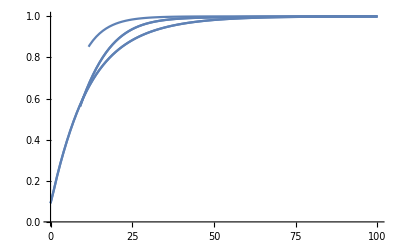

```mathematica
Show[ListLinePlot[p[1.0]],ListLinePlot[p[2.0]],ListLinePlot[p[3.0]],ListLinePlot[p[4.0]],ListLinePlot[p[5.0]]]
```

```mathematica
(*fidelity*)
atom=2;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=KroneckerProduct[{{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}/3,{{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}];
init=KroneckerProduct[{{1, 0, 0}, {0, 0, 0}, {0, 0, 0}},{{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}];
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];



r[1]=0λ0;
r[2]=0.5 λ0;
r[3]=-2λ0;
ratio=0.5;

δω=20;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])];(*KroneckerDelta[j,l]; atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])](*KroneckerDelta[j,5-l]*); 
Λ[i_,j_,k_,l_]:=√(γ[j]γ[l])Sin[k0(r[i]-r[k])]/2;

solsq=NDSolve[{ρ'[t]==-0.5sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(ch^2)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-I Sum[ Λ[i,j,k,l](σ[i,j,1].σ[k,l,0].ρ[t]-ρ[t].σ[i,j,1].σ[k,l,0])Exp[I(ω[j]-ω[l])t],{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,1000}];
ss=Chop[ρ[t]/.solsq/.t->1000,10^-5][[1]];
ss//MatrixForm
```

(0.488328 | 0 | -0.320596 | 0 | 0 | 0 | -0.320596 | 0 | 0.210477
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.320596 | 0 | 0.210477 | 0 | 0 | 0 | 0.210477 | 0 | -0.138182
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.320596 | 0 | 0.210477 | 0 | 0 | 0 | 0.210477 | 0 | -0.138182
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.210477 | 0 | -0.138182 | 0 | 0 | 0 | -0.138182 | 0 | 0.0907186)

```mathematica
(*fidelity-r*)
atom=2;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
(*init=KroneckerProduct[{{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}/3,{{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}];*)
init=KroneckerProduct[{{0, 0, 0}, {0, 0, 0}, {0, 0, 1}},{{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}];
Do[λ0=1;k0=2Pi/λ0;
rr=x;
sh=Sinh[rr];
ch=Cosh[rr];



r[1]=0λ0;
r[2]=1 λ0;
r[3]=-2λ0;
ratio=0.5;

δω=20;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])];(*KroneckerDelta[j,l]; atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])](*KroneckerDelta[j,5-l]*); 
Λ[i_,j_,k_,l_]:=√(γ[j]γ[l])Sin[k0(r[i]-r[k])]/2;

solsq=NDSolve[{ρ'[t]==-0.5sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(ch^2)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-I Sum[ Λ[i,j,k,l](σ[i,j,1].σ[k,l,0].ρ[t]-ρ[t].σ[i,j,1].σ[k,l,0])Exp[I(ω[j]-ω[l])t],{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,1000}];
ss=Chop[ρ[t]/.solsq/.t->1000,10^-5][[1]];
ss//MatrixForm;
p[10x]=Table[{temp=MatrixPower[(ρ[t]/.solsq/.t->n)[[1]],0.5];sig=KroneckerProduct[{{(sh^2 γ[2])/(ch^2 γ[3]+sh^2 γ[2]), 0, -(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2])}, {0, 0, 0}, {-(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2]), 0, (ch^2 γ[3])/(ch^2 γ[3]+sh^2 γ[2])}},{{(sh^2 γ[2])/(ch^2 γ[3]+sh^2 γ[2]), 0, -(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2])}, {0, 0, 0}, {-(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2]), 0, (ch^2 γ[3])/(ch^2 γ[3]+sh^2 γ[2])}}];n,Re[(Tr[MatrixPower[(temp.sig.temp),0.5]])]^2},{n,0,100}],{x,0.5,1.5,0.5}]
```

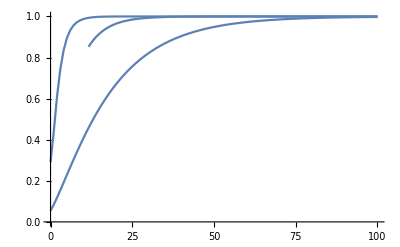

```mathematica
Show[ListLinePlot[p[5.0],PlotRange->All],ListLinePlot[p[10.0]],ListLinePlot[p[15.0]]]
```

```mathematica
Export["r12.dat",Join[p[5.0],p[10.0],p[15.0],2]]
```

r12.dat

```mathematica
(*fidelity-r*)
atom=2;(*num of atoms*)
level=3; (*1 is ground*)
dim=level^atom;(*dimension in Hilbert space*)
(*notation: Matrix[1,1] is excited state, Matrix[n,n] is ground state, so i col/row corresponds to |dim-i> state*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
(*raising/lowering without factor √n, 1 atom, xij[i][i+1] is raising from i+1 to i, xij[i+1,i] is lowering*)
ithexcited[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[Table[t,{t,0,level-1}],{digit}],kth->{level-1}]];
(*digit is total atom num, here ithexcited gives all possible state for ith = excited, i.e.: {|...ai=level-1...>}*)
Do[σ[i,j,1]=Sum[xij[dim-(j-1)*level^(atom-i)-x, dim-(j-2)*level^(atom-i)-x ]Boole[IntegerDigits[x,level,atom][[i]]==0],{x,0,dim-1}],{i,1,atom},{j,2,level}]
(*excite ith atom, from |a1a2...ai=j-2...an> to |a1a2...ai+1=j-1...an>, diff is level^(n-i), from (j-2)*level^(n-i)+x to (j-1)*level^(n-i)+x, x from |0000> to |level-1,..>. and x's i digit is 0, so ai is unchanged
j =2 means excite to 2 or decay from 2. In matrix, it is from dim-(j-2)*level^(n-i)-x to dim-(j-1)*level^(n-i)-x*)
Do[σ[i,j,0]=Transpose[σ[i,j,1]],{i,1,atom},{j,1,level}];
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
(*init=KroneckerProduct[{{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}/3,{{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}];*)
init=KroneckerProduct[{{0, 0, 0}, {0, 0, 0}, {0, 0, 1}},{{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}];
Do[λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];



r[1]=0λ0;
r[2]=1 λ0;
r[3]=-2λ0;
ratio=x;

δω=20;
ω0=100;
ω[2]=ω0+δω;
ω[3]=ω0-δω;

γ[2]=1/ratio;
γ[3]=ratio;
k0=2Pi/λ0;
γ[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])];(*KroneckerDelta[j,l]; atom i's j level, atom k's l level*)
γp[i_,j_,k_,l_]:=√(γ[j]γ[l])Cos[k0(r[i]-r[k])](*KroneckerDelta[j,5-l]*); 
Λ[i_,j_,k_,l_]:=√(γ[j]γ[l])Sin[k0(r[i]-r[k])]/2;

solsq=NDSolve[{ρ'[t]==-0.5sh ch Sum[Exp[I 2(α-0.5)(ω[j]+ω[l]-2ω0)t]γp[i,j,k,l](ρ[t].σ[i,j,α].σ[k,l,α]+σ[i,j,α].σ[k,l,α].ρ[t]-2σ[k,l,α].ρ[t].σ[i,j,α]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level},{α,0,1}]-0.5(ch^2)Sum[Exp[I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,1].σ[k,l,0]+σ[i,j,1].σ[k,l,0].ρ[t]-2σ[k,l,0].ρ[t].σ[i,j,1]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-0.5 sh^2Sum[Exp[-I (ω[j]-ω[l])t]γ[i,j,k,l](ρ[t].σ[i,j,0].σ[k,l,1]+σ[i,j,0].σ[k,l,1].ρ[t]-2σ[k,l,1].ρ[t].σ[i,j,0]),{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}]-I Sum[ Λ[i,j,k,l](σ[i,j,1].σ[k,l,0].ρ[t]-ρ[t].σ[i,j,1].σ[k,l,0])Exp[I(ω[j]-ω[l])t],{i,1,atom},{j,2,level},{k,1,atom},{l,2,level}],ρ[0]==init},slnn,{t,0,1000}];
ss=Chop[ρ[t]/.solsq/.t->1000,10^-5][[1]];
ss//MatrixForm;
p[10x]=Table[{temp=MatrixPower[(ρ[t]/.solsq/.t->n)[[1]],0.5];sig=KroneckerProduct[{{(sh^2 γ[2])/(ch^2 γ[3]+sh^2 γ[2]), 0, -(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2])}, {0, 0, 0}, {-(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2]), 0, (ch^2 γ[3])/(ch^2 γ[3]+sh^2 γ[2])}},{{(sh^2 γ[2])/(ch^2 γ[3]+sh^2 γ[2]), 0, -(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2])}, {0, 0, 0}, {-(ch sh √(γ[2]γ[3]))/(ch^2 γ[3]+sh^2 γ[2]), 0, (ch^2 γ[3])/(ch^2 γ[3]+sh^2 γ[2])}}];n,Re[(Tr[MatrixPower[(temp.sig.temp),0.5]])]^2},{n,0,100}],{x,0.1,1,0.4}]
```

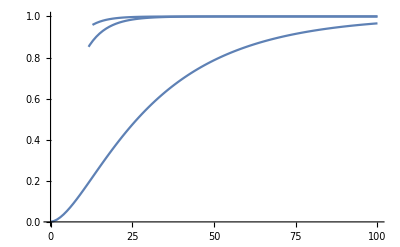

```mathematica
Show[ListLinePlot[p[1],PlotRange->{0,1}],ListLinePlot[p[5.0]],ListLinePlot[p[9.]]]
```

```mathematica
Export["ratio.dat",Join[p[1.],p[5.0],p[9.],2]]
```

ratio.dat